```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

{{x→-0.889352},{x→-0.173136+0.695565 ⅈ},{x→-0.173136-0.695565 ⅈ},{x→0.548022},{x→-0.0623972}}

{{x→-0.25},{x→-0.25},{x→0.},{x→0.}}

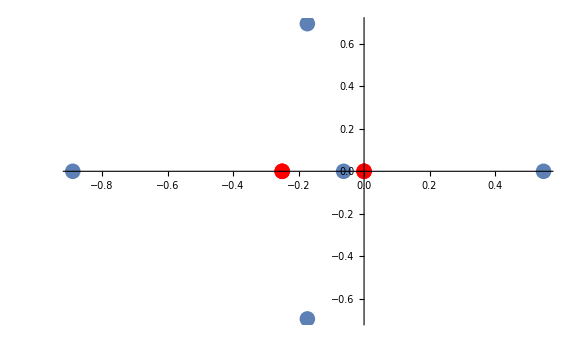

```mathematica
potential=Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x]/.{δ->0.5,β->0};
zeros=NSolve[potential[x]==0,x]
poles=NSolve[potential[x]^-1==0,x]
(*ListPlot[Table[{Re[x/.poles[[i]]],Im[x/.poles[[i]]]},{i,1,Length[poles]}],PlotStyle->Red]*)
Show[ListPlot[Table[{Re[x/.zeros⟦i⟧],Im[x/.zeros⟦i⟧]},{i,1,Length[zeros]}]],ListPlot[Table[{Re[x/.poles⟦i⟧],Im[x/.poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red],ImageSize->Large]
```

{{x→-1.17611},{x→0.33281+0.933047 ⅈ},{x→0.33281-0.933047 ⅈ},{x→0.954086},{x→-0.599776},{x→0.21089},{x→-0.0273535+0.165218 ⅈ},{x→-0.0273535-0.165218 ⅈ}}

{{x→0.+0.5 ⅈ},{x→0.+0.5 ⅈ},{x→0.-0.5 ⅈ},{x→0.-0.5 ⅈ},{x→0.25},{x→0.},{x→0.}}

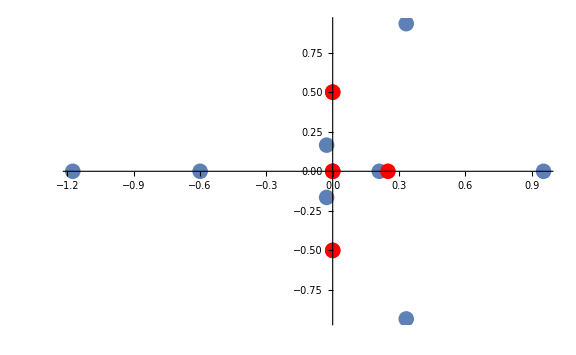

```mathematica
potential=Q[-1/x(x^2-β^2)/(x^2+β^2),-(x+δ^2-β/x-(2β δ)/(x-β^2)),x]/.{δ->0.5,β->0.5};
zeros=NSolve[potential[x]==0,x]
poles=NSolve[potential[x]^-1==0,x]
(*ListPlot[Table[{Re[x/.poles[[i]]],Im[x/.poles[[i]]]},{i,1,Length[poles]}],PlotStyle->Red]*)
Show[ListPlot[Table[{Re[x/.zeros⟦i⟧],Im[x/.zeros⟦i⟧]},{i,1,Length[zeros]}],PlotRange->Full],ListPlot[Table[{Re[x/.poles⟦i⟧],Im[x/.poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red],ImageSize->Large]
```

```mathematica
Residue[Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x][z],{z,0}]
Residue[Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x][z],{z,-δ^2}]
```

(1-2 β δ+2 β^2 δ^2)/(2 δ^2)

(-1+2 β δ)/(2 δ^2)

```mathematica
Residue[Q[-1/x(x^2-β^2)/(x^2+β^2),-(x+δ^2-β/x-(2β δ)/(x-β^2)),x][z],{z,0}]
Residue[Q[-1/x(x^2-β^2)/(x^2+β^2),-(x+δ^2-β/x-(2β δ)/(x-β^2)),x][z],{z,β}]
Residue[Q[-1/x(x^2-β^2)/(x^2+β^2),-(x+δ^2-β/x-(2β δ)/(x-β^2)),x][z],{z,ⅈ β}]
Residue[Q[-1/x(x^2-β^2)/(x^2+β^2),-(x+δ^2-β/x-(2β δ)/(x-β^2)),x][z],{z,-ⅈ β}]
```

β

0

-ⅈ/(4 β)

ⅈ/(4 β)